# Infant Mortality and Economic Development

Arav Bhardwaj

North Carolina School of Science and Mathematics

2022/10/27

## Research Question

How does the economic development of a country relate to infant mortality?

## Background

Infant mortality is defined as the death of a child under the age of 1, and is measured as a probability of deaths per thousand live births (also known IMR, or infant mortality rate). It is a key indicator of the overall health of a society. According to the CDC, in 2020, the infant mortality rate in the United States was 5.4 deaths per 1,000 live births. Reduction of infant mortality is one of the United Nations Sustainable Development Goals (SGDs).

There are three main types of infant mortality: prenatal (death up to one week after childbirth), neonatal (death within 28 days after childbirth), and postneonatal (death between 29 days to a year after childbirth. In developing countries, neonatal childbirth comprises 40 to 60 percent of infant mortality, and is primarily caused by inadequate access to healthcare, both during and after pregnancy. The greatest reduction of infant mortality occurs in countries which already have a low infant mortality rate, as common causes are preventable with low-cost measures.

In developed countries, such as the United States, the leading causes of infant mortality include pneumonia, birth asphyxia, and birth defects. However, at a global level, other factors, such as living standards, political and medical infrastructure, and education can have a great effect on infant mortality. All of these factors fall under the umbrella of economic development, and this lab takes a visual approach to identify trends linking economic development to infant mortality.

## Methodology

First, I selected nine countries and created a bar chart of the infant mortality fractions for each country. I then chose GDP per capita the main indicator of a particular country’s economic development, and created another bar chart. I noticed a trend: lower GDP per capita corresponded to a higher rate of infant mortality. To further explore this, I created a scatter plot of all the countries on the globe, plotting infant mortality against GDP per capita. The scatter plot showed that as GDP per capita increases, the infant mortality fraction decreases. To corroborate my findings, I used two other indicators of economic prosperity: export value and national income.

## Code/Computational Approach

This is where you will put your code.

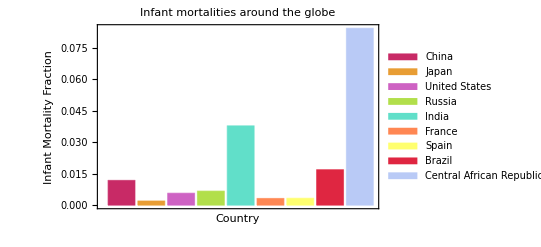

```mathematica
(*I've picked nine countries to examine*)
countries = {Entity["Country","China"], Entity["Country","Japan"], Entity["Country","UnitedStates"], Entity["Country","Russia"], Entity["Country","India"], Entity["Country","France"], Entity["Country","Spain"], Entity["Country","Brazil"], Entity["Country","CentralAfricanRepublic"]};
(* First, I want a bar chart to visualize the infant mortality fractions in each of these countries *)
infantMortality = CountryData[#, "InfantMortalityFraction"] &/@ countries;
BarChart[
{infantMortality}, ChartStyle-> 54, ChartLegends->{countries},
PlotLabel->"Infant mortalities around the globe",
Frame -> True, 
FrameLabel -> {"Country", "Infant Mortality Fraction"}, 
RotateLabel->True
]
```

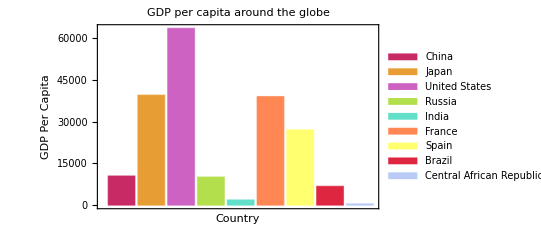

```mathematica
(* Now, I'll plot the GDP per capita of each country as an indicator of economic development *)
GDP = CountryData[#, "GDPPerCapita"] &/@ countries;
BarChart[
{GDP}, ChartStyle-> 54, ChartLegends->{countries},
PlotLabel->"GDP per capita around the globe",
Frame -> True, 
FrameLabel-> {"Country", "GDP Per Capita"},
RotateLabel->True
]
```

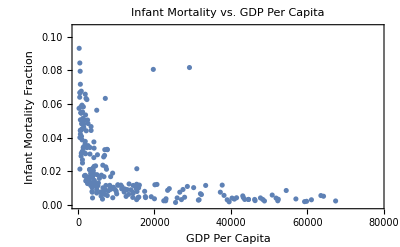

```mathematica
(* Let's do a scatter plot of Infant Mortality vs. GDP per capita of ALL the countries *)
allCountries = CountryData[];
GDPAll = CountryData[#, "GDPPerCapita"] &/@ allCountries;
infantMortalityAll = CountryData[#, "InfantMortalityFraction"] &/@ allCountries;
GDPNum = QuantityMagnitude[GDPAll];
infantMortalityNum = QuantityMagnitude[infantMortalityAll];
data = Thread[{GDPNum, infantMortalityNum}];
ListPlot[data, 
PlotLabel->"Infant Mortality vs. GDP Per Capita", 
Frame -> True, 
FrameLabel->{"GDP Per Capita","Infant Mortality Fraction"}, 
RotateLabel->False]
```

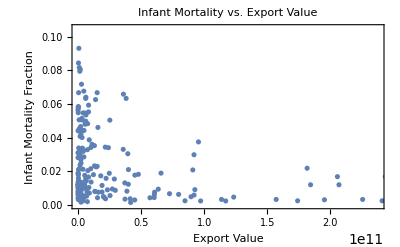

```mathematica
(* I want to see if other indicators of economic development agree with the trend above *)
exportval = CountryData[#, "ExportValue"] &/@ allCountries;
exportvalNum = QuantityMagnitude[exportval];
data2 = Thread[{exportvalNum, infantMortalityNum}];
ListPlot[data2,
PlotLabel -> "Infant Mortality vs. Export Value",
Frame -> True,
FrameLabel -> {"Export Value", "Infant Mortality Fraction"},
RotateLabel -> False]
```

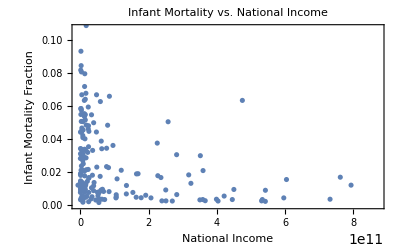

```mathematica
nationalIncome = CountryData[#, "NationalIncome"] &/@ allCountries;
nationalIncomeNum = QuantityMagnitude[nationalIncome];
data3 = Thread[{nationalIncome, infantMortalityNum}];
ListPlot[data3,
PlotLabel -> "Infant Mortality vs. National Income",
Frame -> True,
FrameLabel -> {"National Income", "Infant Mortality Fraction"},
RotateLabel -> False]
```

## Discussion

The research shows a strong relationship between economic development and infant mortality. Using three different indicators, GDP per capita, export value, and national income, the research shows that less economically prosperous countries have higher infant mortality fractions. Lower economic development corresponds to lower nutrition and inadequate access to medical resources, leading to higher rates of infant mortality. Thus, one of the best ways to reduce infant mortality on a global scale is by targeting change at a systemic level.